## Белко Владислав, ПО-5

Лабораторная работа №7.

### Basic Statistics

```mathematica
BVvar= RandomInteger[80,10]
```

{45,49,0,56,42,3,3,44,34,32}

↓Находим среднее арифметическое↓

```mathematica
Mean[BVvar] // N
```

30.8

↓Находим среднее значение в списке (сортировка -> среднее)↓

```mathematica
Median[BVvar]
```

38

↓Находим максимальный элемент списка↓

```mathematica
Max[BVvar]
```

56

↓Находим дисперсию. Среднее арифметическое(СА), вычитаем из каждого элемента списка СА,  делаем сумму квадратов из полученных чисел, делим на BVvar.count - 1↓

```mathematica
Variance[BVvar] // N
```

441.511

↓Находим выборочное стандартное отклонение элементов в списке. Эквивалентно  Sqrtpaclet:ref/Sqrt[Variancepaclet:ref/Variance[…]].↓

```mathematica
StandardDeviation[BVvar] // N
```

21.0122

↓Находим медиану с “разбросом” ↓

```mathematica
{39,25,23,7,33,59,46,21,7,16}
```

```mathematica
Quantile[BVvar,1/3]
```

32

↓Сумма элементов списка↓

```mathematica
Total[BVvar]
```

308

### Descriptive Statistics

Mean, Median, Quantile уже были рассмотрены.
↓Выдает нам список наиболее часто повторяющихся цифр↓

```mathematica
Commonest[BVvar]
```

{3}

↓Находим среднее геометрическое чисел списка -> (перемножение всех чисел списка) ^ (1 / количество чисел)↓

```mathematica
GeometricMean[BVvar] // N
```

22.4874

↓Находим среднее гармоническое. Количество элементов делим на сумму всех 1/элемент ↓

```mathematica
HarmonicMean[BVvar] //N
```

17.4233

↓Находим среднее квадратичное. Берём корень из суммы квадратов элементов, делённый на количество элементов↓

```mathematica
RootMeanSquare[BVvar]
```

√1346

↓Находим усечённое среднее. Берём весь отсортированный список и отсекаем с двух сторон то количество чисел, которому равно 0.1 (в данном случае) от всего количества. ↓

```mathematica
TrimmedMean[BVvar,0.15] // N
```

31.5

↓Делаем тоже самое, только теперь первое число отсекаем от минимальных, а второе число отсекаем от максимальных.↓

```mathematica
TrimmedMean[BVvar,{0.3,0.1}]
```

41

↓Находим медиану с “разбросом” ↓

```mathematica
Quantile[BVvar,0.2]
```

3

↓Находим среднее арифметическое. Вычитаем из каждого числа найденное, берем по модулю и суммируем получившееся, потом делим на количество чисел.↓

```mathematica
MeanDeviation[BVvar] // N
```

17.28

↓Находим медиану. Вычитаем из всех чисел, берём по модулю все числа, формируем новый список. Находим уже тут медиану.↓

```mathematica
MedianDeviation[BVvar]
```

9

```mathematica
12
Discrete Distributions
```

↓Находим межквартильный диапазон, эквивалентно Quantilepaclet:ref/Quantile[BVvar,3/4]-Quantilepaclet:ref/Quantile[BVvar,1/4]↓

```mathematica
InterquartileRange[BVvar]
```

42

↓Находим КвартильОтклонение. Эквивалентно InterquartileRangepaclet:ref/InterquartileRange[BVvar]/2↓

```mathematica
QuartileDeviation[BVvar]
```

21

↓Находим коэффициент асимметрии для элементов в списке.↓

```mathematica
Skewness[BVvar]
```

-272211/(4967 √9934)

↓Находим коэффициент эксцесса для элементов в списке.↓

```mathematica
Kurtosis[BVvar]
```

84198041/49342178

↓Находим коэффициент перекоса квартилей для элементов в списке.
Положительное значение перекоса квартилей указывает, что медиана ближе к нижнему индексу [q, 1] нижнего квартиля, чем к нижнему индексу [q, 3] верхнего квартиля.
Отрицательное значение перекоса квартилей указывает, что медиана ближе к верхнему квартилю.↓

```mathematica
QuartileSkewness[BVvar]
```

-2/3

```mathematica
7/23
```

↓Образует свертку ядра {a, b, c} со списком чисел↓

```mathematica
ListConvolve[{a, b, c},{1,3, 5, 7, 9}]
```

{5 a+3 b+c,7 a+5 b+3 c,9 a+7 b+5 c}

```mathematica
12
Моделирование методом Монте - Карло
```

Пусть у нас есть группа из 48 человек ровестников одного года рождения (например у всех 2002 год рождения). Какова вероятность того, что в группе попадутся те, у кого дни рождения совпадают?

```mathematica
groupMonteKarlo[childrends_, experiments_]:=Module[{a=childrends,b=experiments},
counterPeoplesInGroup=a;
counterExperiments = b;
counterSuccessFullExperiments=0;
For[i=1,i<=counterExperiments,i++,
lst=Table[Random[Integer,{1,365}],{i,1,counterPeoplesInGroup}];If[Length[lst]!=Length[DeleteDuplicates[lst]],counterSuccessFullExperiments+=1]
];
Print["Количество экспериментов: ", counterExperiments];
Print["Количество экспериментов, в которых даты рождения совпали ", counterSuccessFullExperiments];
Print["Вероятность, что в группе из ",counterPeoplesInGroup, " человек будут те, у которых день рождения совпадает: p = ", 
counterSuccessFullExperiments, " / ", counterExperiments, " * 100% = ", N[counterSuccessFullExperiments/counterExperiments * 100], "%"];
N[counterSuccessFullExperiments/counterExperiments]
]
```

```mathematica
groupMonteKarlo[24,100000]
```

Количество экспериментов: 100000

Количество экспериментов, в которых даты рождения совпали 53905

Вероятность, что в группе из 24 человек будут те, у которых день рождения совпадает: p = 53905 / 100000 * 100% = 53.905%

0.53905

```mathematica
groupMonteKarlo[48,100000]
```

Количество экспериментов: 100000

Количество экспериментов, в которых даты рождения совпали 96085

Вероятность, что в группе из 48 человек будут те, у которых день рождения совпадает: p = 96085 / 100000 * 100% = 96.085%

0.96085

Вычислить площадь фигуры x^2+y^2=R^2, у которой есть ограничения x>=0 и y>=0, где R дано.

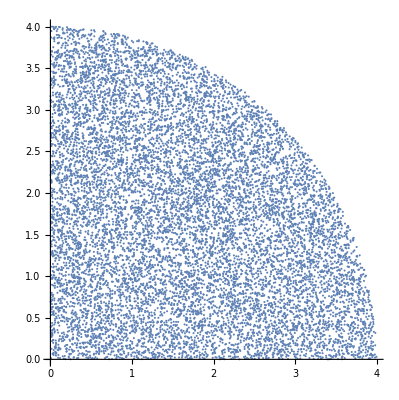

Методом Монте-Карло получили площадь равную 12.626 (в оригинале она равна 12.5664)

```mathematica
xmin=-5;
xmax=5;
ymin=-5;
ymax=5;
R=4;
counter=0;
counterExperiments=100000;
lst={};
For[i=1,i<=counterExperiments,i++,
x=Random[Real,{xmin,xmax}];
y=Random[Real,{ymin,ymax}];
If[x^2+y^2<=R^2 && y>=0&&x>=0,
counter+=1;
lst=Join[{{x,y}},lst]
]
]
squareMonteKarlo=N[(Abs[xmin]+Abs[xmax])*(Abs[ymin]+Abs[ymax])*counter/counterExperiments];
squareOriginal=N[Pi*R^2/2/2];
ListPlot[lst,AspectRatio->Automatic]
Print["Методом Монте-Карло получили площадь равную ", squareMonteKarlo, " (в оригинале она равна ", squareOriginal, ")"]
```

Найти площадь фигуры на промежутке от -7 до 7 заданой формулами sin(x) и y>0

Методом Монте-Карло получили площадь равную 3.92372

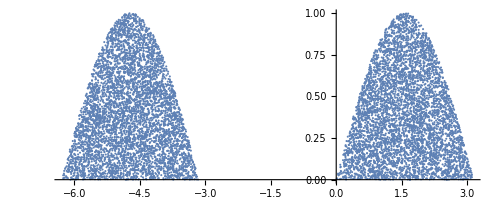

```mathematica
xmin=-2Pi;
xmax=2*Pi;
ymin=-1.5;
ymax=1.5;
counter=0;
counterExperiments=100000;
lst={};
For[i=1,i<=counterExperiments,i++,
x=Random[Real,{xmin,xmax}];
y=Random[Real,{ymin,ymax}];
If[Sin[x]>=y && y>=0,
counter+=1;
lst=Join[{{x,y}},lst]]
]
squareMonteKarlo=N[(Abs[xmin]+Abs[xmax])*(Abs[ymin]+Abs[ymax])*counter/counterExperiments];
Print["Методом Монте-Карло получили площадь равную ", squareMonteKarlo];
ListPlot[lst,AspectRatio->Automatic]
```